# Outliers Detection with Clustering

```mathematica
clustersNo = FindClusters[reducedOxyNo80[[1;;10,1]],Method->"MeanShift"];
```

```mathematica
Dimensions[clustersNo]
```

{3}

```mathematica
Dimensions[clustersNo[[1]]]
Dimensions[clustersNo[[2]]]
Dimensions[clustersNo[[3]]]
```

{5,80}

{4,80}

{1,80}

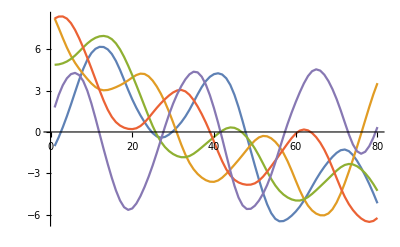
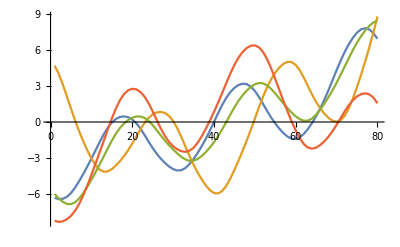
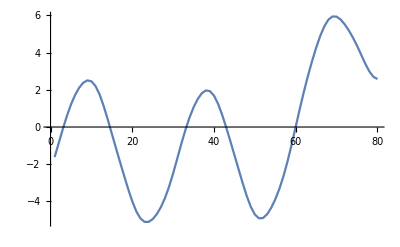
{-Graphics-→5,-Graphics-→4,-Graphics-→1}

```mathematica
Table[ListLinePlot[clustersNo[[i]]]-> Length[clustersNo[[i]]],{i,Dimensions[clustersNo][[1]]}]
```

```mathematica
clusteredOxyNo = clustersNo[[1]];
```

```mathematica
clustersYes = FindClusters[reducedOxyYes80[[1;;10,1]],Method->"MeanShift"];
Dimensions[clustersYes]
```

{3}

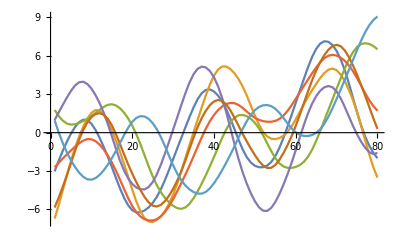
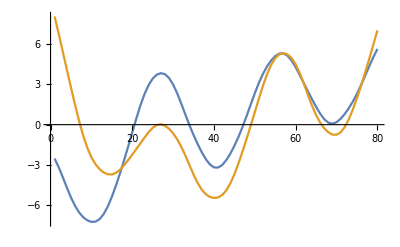
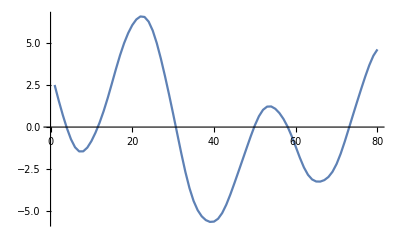
{-Graphics-→7,-Graphics-→2,-Graphics-→1}

```mathematica
Table[ListLinePlot[clustersYes[[i]]]-> Length[clustersYes[[i]]],{i,Dimensions[clustersYes][[1]]}]
```

{9,80}

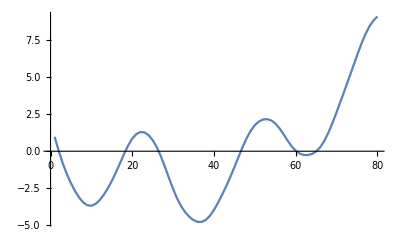

```mathematica
clusteredOxyYes = Join[clustersYes[[1]],clustersYes[[2]]];
Dimensions[clusteredOxyYes]
ListLinePlot[clusteredOxyYes[[7]]]
```

```mathematica
clustData = Join[Table[clusteredOxyYes[[i]]->"Yes",{i,Length[clusteredOxyYes]}],Table[clusteredOxyNo[[i]]->"No",{i,Length[clusteredOxyNo]}]];
```

```mathematica
clustData//Dimensions
```

{14}

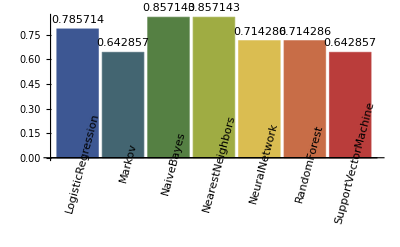

```mathematica
autoML[clustData]
```

```mathematica
autoMLAccurate[clustData]
```

$Aborted

## Archetypal on the reduced outliers set

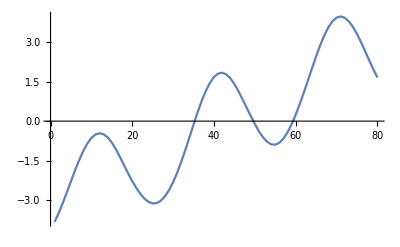

```mathematica
nooutMeanArchetypalYes = Mean[clusteredOxyYes[[All]]];
nooutMeanArchetypalNo = Mean[clusteredOxyNo[[All]]];
ListLinePlot[nooutMeanArchetypalYes]

l1DistVect[signal_List] := {ManhattanDistance[signal,nooutMeanArchetypalYes],ManhattanDistance[signal,nooutMeanArchetypalNo]}
```

```mathematica
dataDistArchDriftL1 = Join[Table[l1DistVect[clusteredOxyNo[[x]]]->"No",{x,Length[clusteredOxyNo]}],Table[l1DistVect[clusteredOxyYes[[x]]]->"Yes",{x,Length[clusteredOxyYes]}]];
```

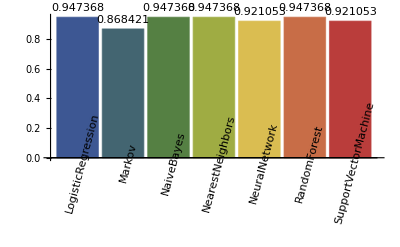

```mathematica
autoML[dataDistArchDriftL1]
```